### Cubic Lattice_ Simple Cubic

#### Define the Hamiltonian

```mathematica
H[kx_,ky_,kz_]:=-2 (Cos[kx]+Cos[ky]+Cos[kz]);
```

#### Define the Dispersion Function

```mathematica
F[kx_,ky_,kz_]:=H[kx,ky,kz];
```

#### Plot The dispersion Function Along high symmetry Points Loop (X-Γ-M-R-Γ-X-M)

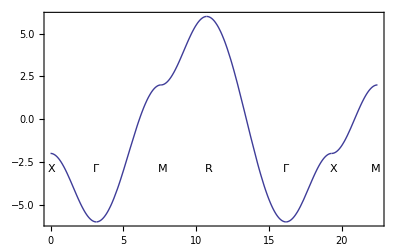

```mathematica
Plot[Piecewise[{{F[Pi-t,0,0],t≥0&&t<Pi},{F[(t-Pi)/Sqrt[2],(t-Pi)/Sqrt[2],0],t≥Pi&&t<(1+Sqrt[2])Pi},{F[Pi,Pi,t-(1+Sqrt[2])Pi],t≥(Sqrt[2]+1)Pi&&t<(Sqrt[2]+2)Pi},{F[Pi-(t-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(t-(2+Sqrt[2])Pi)/Sqrt[3],Pi-(t-(2+Sqrt[2])Pi)/Sqrt[3]],t≥(2+Sqrt[2])Pi&&t<(2+Sqrt[2]+Sqrt[3])Pi},{F[t-(2+Sqrt[2]+Sqrt[3])Pi,0,0],t≥(2+Sqrt[2]+Sqrt[3])Pi&&t<(3+Sqrt[2]+Sqrt[3])Pi},{F[Pi,t-(3+Sqrt[2]+Sqrt[3])Pi,0],t≥(3+Sqrt[2]+Sqrt[3])Pi&&t≤(4+Sqrt[2]+Sqrt[3])Pi}}],{t,0,(4+Sqrt[2]+Sqrt[3])Pi},GridLines->{{{Pi,Dashed},{(1+Sqrt[2])Pi,Dashed},{(Sqrt[2]+2)Pi,Dashed},{(2+Sqrt[2]+Sqrt[3])Pi,Dashed},{(3+Sqrt[2]+Sqrt[3])Pi,Dashed},{(4+Sqrt[2]+Sqrt[3])Pi,Dashed}},{}},Epilog->{Inset["X",{0.05,0.08-3}],Inset["Γ",{Pi,0.08-3}],Inset["M",{(1+Sqrt[2])Pi+0.15,0.08-3}],Inset["R",{(2+Sqrt[2])Pi+0.15,0.08-3}],Inset["Γ",{(2+Sqrt[2]+Sqrt[3])Pi,0.08-3}],Inset["X",{(3+Sqrt[2]+Sqrt[3])Pi+0.15,0.08-3}],Inset["M",{(4+Sqrt[2]+Sqrt[3])Pi-0.15,0.08-3}]},Frame->True]
```